```mathematica
(*TE and TM Reflection coefficients, denominators *)
R1 = (p - √(p^2 + χ))/(p + √(p^2+χ));
R2[p_,χ_]:=  ((1+χ)p - √(p^2 + χ))/((1+χ)p + √(p^2+χ));
```

```mathematica
LifshitzInt[χ_]:=NIntegrate[(p^2/(-1+(ⅇ^(2 p u) (p+√(p^2+χ))^2)/((p-√(p^2+χ))^2))+p^2/(-1+(ⅇ^(2 p u) (p (1+χ)+√(p^2+χ))^2)/((p (1+χ)-√(p^2+χ))^2)))u^3,{p,1,∞},{u,0,∞}]

LogIntTE[χ_] :=-NIntegrate[p u^2Log[1-((p -√(p^2+χ))/(p +√(p^2+χ)))^2 ⅇ^(-2 p u)] ,{p,1,∞},{u,0,∞}]180/π^4
LogIntTM[χ_] := -NIntegrate[p u^2 Log[ 1 -((p (1+χ)-√(p^2+χ))/(p (1+χ)+√(p^2+χ)))^2  ⅇ^(-2 p u)],{p,1,∞},{u,0,∞}]180/π^4

LogInt[χ_]:=LogIntTM[χ]+LogIntTE[χ]
```

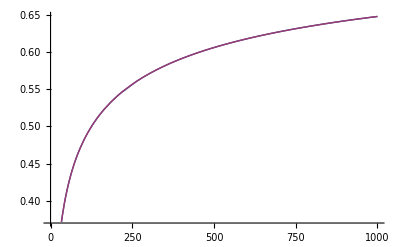

```mathematica
Plot[{LifshitzInt[χ],SchwingerInt[χ]},{χ,10^-3,10^3}]
```

```mathematica
N[2^20]
```

1.04858×10^6

```mathematica
ηTE[χ_]:=1/6+1/χ-(√(1+χ))/(2χ)-ArcSinh[√χ]/(2 χ^(3/2))
ηTE1[χ_]:=1/3+2/χ-(√(χ(χ+1)))/χ^(3/2)-Log[1+2χ+2 √(χ(χ+1))]/(4 χ^(3/2))-ArcSinh[√χ]/(2 χ^(3/2))
```

```mathematica
N[{ηTE[x],ηTE1[x]/2}/.{x->.31}]
```

{0.00700204,0.00700204}

```mathematica
Table[{LogIntTE[10^n]},{n,0,6}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

```mathematica
{{0.003313854418629076``},{0.05112879141955042},{0.1882499465516168},{0.3315149783012317},{0.42236821715539724},{0.46749143986180575},{0.48717558087443796}}
```

```mathematica
0.05112879141955042``
```

```mathematica
Ntot = 160; s2=2^1/4;
dataAtom=Table[{s2^((n -Ntot/2)),ηTE[s2^(n-Ntot/2)]}, {n,Ntot}];
Export["/home/jonathan/papers/worldline1/fig/data/TE_atom_anlt.dat",N[dataAtom],"TSV"]
```

/home/jonathan/papers/worldline1/fig/data/TE_atom_anlt.dat

```mathematica
s2=Sqrt[Sqrt[2]]
Ntot = 160; 
data1=Table[{s2^(n -Ntot/4),LogIntTE[s2^(n-Ntot/2)]}, {n,Ntot}];
Export["/home/jonathan/work/casimir/f90_code/scalar_TE_monte/TE_2wall_anlt_interp.dat",N[data1],"TSV"]
```

```mathematica
Series[LogIntTE[x],{x,0,1}]
```

NIntegrate::inumr: The integrand p\ u^2\ Log[1 - ⅇ^-2\ p\ u\ (p - Power[« 2 »])^2/(p + √Plus[« 2 »])^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 1.}, {∞, 0.}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in u near {u} = {8.16907×10^224}. NIntegrate obtained 8.58263912306054×10^27949 and 8.58263912306054×10^27949 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {8.16907×10^224}. NIntegrate obtained 7.36616943166895×10^55899 and 7.36616943166895×10^55899 for the integral and error estimates.

(1.36117736406921×10^55900 p (-p+√(p^2)) u^2 x)/(√(p^2) (p+√(p^2)) (-p+ⅇ^(2 p u) p+√(p^2)+ⅇ^(2 p u) √(p^2)))+O[x]^2

```mathematica
ListPlot[data1]
```

-Graphics-

```mathematica
s2=Sqrt[Sqrt[2]]
Ntot = 500; 
data1=Table[{s2^(n -Ntot/4),LogIntTE[s2^(n-Ntot/4)]}, {n,Ntot}];
Export["/home/jonathan/work/casimir/f90_code/scalar_TE_monte/TE_2wall_anlt_interp.dat",N[data1],"TSV"]
```

2^(1/4)

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.09951×10^-21 and 1.19338×10^-24 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -6.4019×10^-20 and 1.64578×10^-23 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.21033×10^-19 and 9.82641×10^-23 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

/home/jonathan/work/casimir/f90_code/scalar_TE_monte/TE_2wall_anlt_interp.dat

```mathematica
s2=4
Ntot = 20; 
data1=Table[{s2^(n -Ntot/2),LogIntTE[s2^(n-Ntot/2)]}, {n,Ntot}];
Export["/home/jonathan/papers/worldline1/fig/data/TE_2wall_anlt_short.dat",N[data1],"TSV"]
```

4

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.51619×10^-14 and 5.82139×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -7.27027×10^-13 and 2.39871×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.16402×10^-11 and 6.19181×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

/home/jonathan/papers/worldline1/fig/data/TE_2wall_anlt_short.dat

```mathematica
(*Series Expand integrand*)
IntegrandTE[χ_]:=p u^2Log[1-((p -√(p^2+χ))/(p +√(p^2+χ)))^2 ⅇ^(-2 p u)]
```

```mathematica
Series[IntegrandTE[x],{x,0,2},Assumptions->{p>1}]
```

-((ⅇ^(-2 p u) u^2) x^2)/(4 (p (p+√(p^2))^2))+O[x]^3

```mathematica
Simplify[((ⅇ^(-2 p u) u^2) x^2)/(4 (p (p+√(p^2))^2)),Assumptions->{p>1}]
```

```mathematica
(ⅇ^(-2 p u) u^2 x^2)/(16 p^3)
```

```mathematica
SmallTE[χ_]:=-Integrate[(ⅇ^(-2 p u) u^2 χ^2)/(16 p^3) ,{p,1,∞},{u,0,∞},Assumptions->{χ>0}]180/π^4
```

```mathematica
SmallTE[x]
```

-(9 x^2)/(16 π^4)

```mathematica
Series[IntegrandTE[x],{x,∞,2},Assumptions->{p>1}]
```

p u^2 Log[1-ⅇ^(-2 p u)]+(4 p^2 u^2 √(1/x))/(-1+ⅇ^(2 p u))-(8 (ⅇ^(2 p u) p^3 u^2))/((-1+ⅇ^(2 p u))^2 x)+(2 (-1+18 ⅇ^(2 p u)+15 ⅇ^(4 p u)) p^4 u^2 (1/x)^(3/2))/(3 (-1+ⅇ^(2 p u))^3)-(8 (ⅇ^(2 p u) (1+6 ⅇ^(2 p u)+ⅇ^(4 p u)) p^5 u^2))/((-1+ⅇ^(2 p u))^4 x^2)+O[1/x]^(5/2)